```mathematica
ClearAll["Global`*"]
```

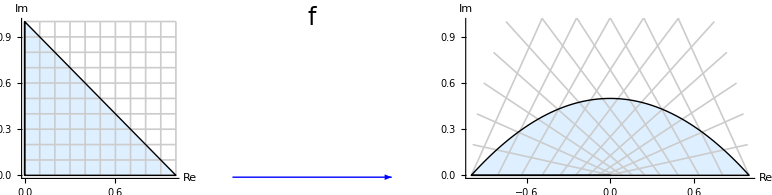

```mathematica
(*Define the complex function*)f[z_]:=z^2

(*Parametrize each side of the triangle*)
side1[t_]:=t+0 I;             (*from 0 to 1*)
side2[t_]:=(1-t)+t I;       (*from 1 to i*)
side3[t_]:=0+t I;             (*from i to 0*)

(*Generate dense points along each side for accurate boundary transformation*)
denseSide1=Table[ReIm[side1[t]],{t,0,1,0.01}];
denseSide2=Table[ReIm[side2[t]],{t,0,1,0.01}];
denseSide3=Table[ReIm[side3[t]],{t,0,1,0.01}];
allTrianglePoints=Join[denseSide1,denseSide2,denseSide3];

(*Transform these points*)
transformedPoints1=ReIm[f/@(denseSide1[[All,1]]+I denseSide1[[All,2]])];
transformedPoints2=ReIm[f/@(denseSide2[[All,1]]+I denseSide2[[All,2]])];
transformedPoints3=ReIm[f/@(denseSide3[[All,1]]+I denseSide3[[All,2]])];
allTransformedPoints=Join[transformedPoints1,transformedPoints2,transformedPoints3];

(*Create grid lines parallel to the axes within the bounding box of the triangle*)
gridLinesX=Table[{{x,0},{x,1}},{x,0,1,0.1}];
gridLinesY=Table[{{0,y},{1,y}},{y,0,1,0.1}];

(*Transform grid lines*)
transformedGridLinesX=Table[{ReIm[f[Complex@@gridLinesX[[i,1]]]],ReIm[f[Complex@@gridLinesX[[i,2]]]]},{i,1,Length[gridLinesX]}];
transformedGridLinesY=Table[{ReIm[f[Complex@@gridLinesY[[i,1]]]],ReIm[f[Complex@@gridLinesY[[i,2]]]]},{i,1,Length[gridLinesY]}];

(*Plot the original and transformed regions with grid lines and filled polygons*)
originalRegion=Graphics[{LightBlue,Polygon[allTrianglePoints],GrayLevel[0.8],Thickness[0.003],Line/@gridLinesX,Line/@gridLinesY,Black,Thick,Line[allTrianglePoints]},Axes->True,PlotRange->{{0,1},{0,1}},AxesLabel->{"Re","Im"}];

transformedRegion=Graphics[{LightBlue,Polygon[allTransformedPoints],GrayLevel[0.8],Thickness[0.003],Line/@transformedGridLinesX,Line/@transformedGridLinesY,Black,Thick,Line[allTransformedPoints]},Axes->True,PlotRange->{{-1,1},{0,1}},AxesLabel->{"Re","Im"}];

(*Define an arrow graphic with the label'f'*)arrowGraphic=Graphics[{Blue,Arrowheads[0.05],Arrow[{{0,0},{0.25,0}}],Black,Text[Style["f",FontSize->24],{0.125,0.05}]},ImageSize->Small (*Adjust the size to fit between the plots*)];

(*Combine the original region,arrow graphic,and transformed region in a row*)
fullGraphic=GraphicsRow[{originalRegion,arrowGraphic,transformedRegion},Spacings->{Scaled[0.1],Scaled[-0.2]},ImagePadding->{{10,10},{10,10}}  (*Increase padding at the top and bottom*)];
fullGraphic
```